Generating bifurcation diagram...

Varying m1 from 1. to 10.

Using seed: 67

Total parameter values: 9001

Total points: 99429

=== Bifurcation Diagram (Local Maxima Method) ===

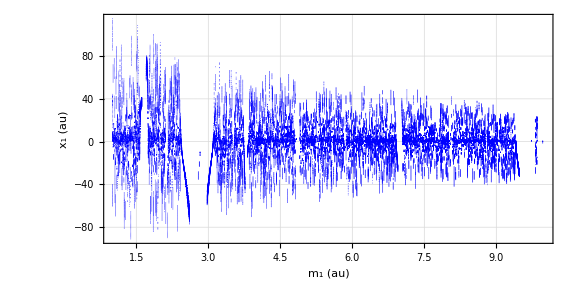

=== Alternative: ListPlot Version ===

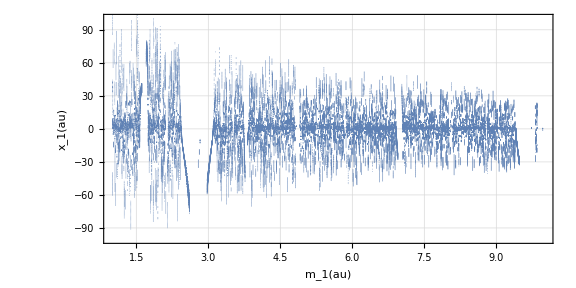

```mathematica
ClearAll["Global`*"];

(*Constants*)
G=4 Pi^2;
conv=1/(1.496*^8*365.25*24*3600);
seed=67;
epsilon=0.01; (*Softening parameter*)

(*Function to get local maxima of x1 position*)
getLocalMaxima[sol_,tStart_,tEnd_]:=Module[{x1Func,samples,peaks},x1Func=x1/. sol[[1]];
(*Sample the function densely*)samples=Table[{t,x1Func[t]},{t,tStart,tEnd,0.1}];
(*Find local maxima by checking neighbors*)peaks=Select[Range[2,Length[samples]-1],samples[[#,2]]>samples[[#-1,2]]&&samples[[#,2]]>samples[[#+1,2]]&];
(*Return the x1 values at peaks*)samples[[peaks,2]]]

(*Function to run simulation for given m1*)
runSimulation[mVar_]:=Module[{q2x,q2y,q3x,q3y,m1,m2,m3,pos1,vel1,pos2,vel2,pos3,vel3,eqs,init,sol,maxDist,maxima},SeedRandom[seed];
(*Initial conditions-fixed seed for reproducibility*)q2x=RandomReal[{5,20}];
q2y=RandomReal[{0,10}];
q3x=RandomReal[{-10,0}];
q3y=RandomReal[{5,20}];
m1=mVar;
m2=1;
m3=1;
(*Positions and velocities*)pos1={0,0};
vel1={0,10}*conv;
pos2={q2x,q2y};
vel2={-10,0}*conv;
pos3={q3x,q3y};
vel3={0,0};
(*Equations with softening*)eqs={x1''[t]==G*m2*(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),y1''[t]==G*m2*(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),x2''[t]==G*m1*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),y2''[t]==G*m1*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),x3''[t]==G*m1*(x1[t]-x3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2),y3''[t]==G*m1*(y1[t]-y3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2)};
(*Initial conditions*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve the system*)sol=Quiet@NDSolve[Join[eqs,init],{x1,y1,x2,y2,x3,y3},{t,0,100},MaxSteps->1000000,Method->"StiffnessSwitching",PrecisionGoal->8,AccuracyGoal->8];
(*If solution failed,return empty list*)If[sol==={},Return[{}]];
(*Check for escapes or extreme behavior*)maxDist=Quiet@Check[Max[Table[Sqrt[(x1[t]/. sol[[1]])^2+(y1[t]/. sol[[1]])^2]+Sqrt[(x2[t]/. sol[[1]])^2+(y2[t]/. sol[[1]])^2]+Sqrt[(x3[t]/. sol[[1]])^2+(y3[t]/. sol[[1]])^2],{t,80,100,2}]],Infinity];
If[maxDist>500,Return[{}]];(*System escaped*)(*Get local maxima of x1 position*)maxima=Quiet@Check[getLocalMaxima[sol,80,100],{}];
If[Length[maxima]==0,Return[{}]];
(*Filter extreme values*)maxima=Select[maxima,-200<=#<=200&];
(*Return points for bifurcation diagram*)Table[{mVar,max},{max,maxima}]]

(*Generate bifurcation data by varying m1*)
mRange=Range[1,10,0.001]; (*m1 from 1 to 10 in steps of 0.05*)
bifurcationData={};

Print["Generating bifurcation diagram..."];
Print["Varying m1 from ",First[mRange]," to ",Last[mRange]];
Print["Using seed: ",seed];
Print["Total parameter values: ",Length[mRange]];

progress=0;
Monitor[Do[data=runSimulation[mVar];
If[Length[data]>0,AppendTo[bifurcationData,data]];
progress++,{mVar,mRange}],ProgressIndicator[progress,{0,Length[mRange]}]];

(*Flatten the data*)
flatData=Flatten[bifurcationData,1];

Print["\nTotal points: ",Length[flatData]];

(*Create the bifurcation diagram*)
bifurcationPlot=Graphics[{PointSize[0.0003],Blue,Point[flatData]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(1\)]\) (au)",FontSize->14, Italic],Style["\!\(\*SubscriptBox[\(x\), \(1\)]\) (au)",FontSize->14, Italic]},PlotRange->{{1,10},Automatic},AspectRatio->1/2,GridLines->Automatic];

Print["\n=== Bifurcation Diagram (Local Maxima Method) ==="];
bifurcationPlot

(*Optional:Create alternative visualization with ListPlot*)


listPlotVersion=ListPlot[flatData,PlotStyle->{PointSize[0.0003]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["m_1(au)",Italic,FontSize->14],Style["x_1(au)",Italic,FontSize->14]},GridLines->Automatic,PlotRange->{{1,10},{100,-100}},(*inverted y-axis*)AspectRatio->1/2,ImageSize->Large,Joined->False];

Print["\n=== Alternative: ListPlot Version ==="];
listPlotVersion
```

```mathematica
orbitPoints[τ2val_,xN_Symbol]:=Module[{vars,init,params,eqs,sol,result,tMax=300,tTrans=250},vars={x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t]};
init=Thread[(vars/. t->0)=={1.1,1.1,1.1,1.1,0,0,0,0}];
params={τ1->11,τ2->τ2val,τ3->2,τ4->0.2,τ5->0.1,τ6->0.1,τ7->0.2};
eqs={x1'[t]==τ1 (x2[t]-x1[t])+x4[t],x2'[t]==τ2 x1[t]-x1[t] x3[t]+x4[t],x3'[t]==x1[t] x2[t]-x3[t]-x4[t]+x7[t],x4'[t]==-τ3 (x1[t]+x2[t])+x5[t],x5'[t]==-x2[t]-τ4 x4[t]+x6[t],x6'[t]==-τ5 (x1[t]+x5[t])+τ4 x7[t],x7'[t]==-τ6 (x1[t]+x6[t]-x8[t]),x8'[t]==-τ7 x7[t]}/. params;
(*Define τ2 range*)τ2Vals=Range[0,400,0.5];

(*Generate datasets for each variable*)
dataX1=Table[orbitPoints[τ2,x1],{τ2,τ2Vals}];


pointsX1=Flatten[dataX1,1];

(*Plot each bifurcation diagram*)
ListPlot[pointsX1,PlotStyle->PointSize[0.0015],Frame->True,FrameLabel->{"C","x₁", Italic},PlotRange->All,AspectRatio->0.6,ImageSize->Large]
```

Generating bifurcation diagram...

Varying m1 from 1. to 10.

Using seed: 12

Total parameter values: 9001

Total points: 112635

=== Bifurcation Diagram (Local Maxima Method) ===

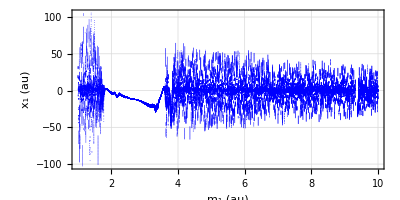

=== Alternative: ListPlot Version ===

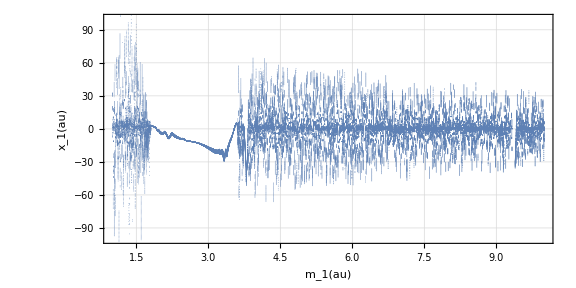

```mathematica
ClearAll["Global`*"];

(*Constants*)
G=4 Pi^2;
conv=1/(1.496*^8*365.25*24*3600);
seed=12;
epsilon=0.01; (*Softening parameter*)

(*Function to get local maxima of x1 position*)
getLocalMaxima[sol_,tStart_,tEnd_]:=Module[{x1Func,samples,peaks},x1Func=x1/. sol[[1]];
(*Sample the function densely*)samples=Table[{t,x1Func[t]},{t,tStart,tEnd,0.1}];
(*Find local maxima by checking neighbors*)peaks=Select[Range[2,Length[samples]-1],samples[[#,2]]>samples[[#-1,2]]&&samples[[#,2]]>samples[[#+1,2]]&];
(*Return the x1 values at peaks*)samples[[peaks,2]]]

(*Function to run simulation for given m1*)
runSimulation[mVar_]:=Module[{q2x,q2y,q3x,q3y,m1,m2,m3,pos1,vel1,pos2,vel2,pos3,vel3,eqs,init,sol,maxDist,maxima},SeedRandom[seed];
(*Initial conditions-fixed seed for reproducibility*)q2x=RandomReal[{5,20}];
q2y=RandomReal[{0,10}];
q3x=RandomReal[{-10,0}];
q3y=RandomReal[{5,20}];
m1=mVar;
m2=1;
m3=1;
(*Positions and velocities*)pos1={0,0};
vel1={0,10}*conv;
pos2={q2x,q2y};
vel2={-10,0}*conv;
pos3={q3x,q3y};
vel3={0,0};
(*Equations with softening*)eqs={x1''[t]==G*m2*(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),y1''[t]==G*m2*(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),x2''[t]==G*m1*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),y2''[t]==G*m1*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),x3''[t]==G*m1*(x1[t]-x3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2),y3''[t]==G*m1*(y1[t]-y3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2)};
(*Initial conditions*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve the system*)sol=Quiet@NDSolve[Join[eqs,init],{x1,y1,x2,y2,x3,y3},{t,0,100},MaxSteps->1000000,Method->"StiffnessSwitching",PrecisionGoal->8,AccuracyGoal->8];
(*If solution failed,return empty list*)If[sol==={},Return[{}]];
(*Check for escapes or extreme behavior*)maxDist=Quiet@Check[Max[Table[Sqrt[(x1[t]/. sol[[1]])^2+(y1[t]/. sol[[1]])^2]+Sqrt[(x2[t]/. sol[[1]])^2+(y2[t]/. sol[[1]])^2]+Sqrt[(x3[t]/. sol[[1]])^2+(y3[t]/. sol[[1]])^2],{t,80,100,2}]],Infinity];
If[maxDist>500,Return[{}]];(*System escaped*)(*Get local maxima of x1 position*)maxima=Quiet@Check[getLocalMaxima[sol,80,100],{}];
If[Length[maxima]==0,Return[{}]];
(*Filter extreme values*)maxima=Select[maxima,-200<=#<=200&];
(*Return points for bifurcation diagram*)Table[{mVar,max},{max,maxima}]]

(*Generate bifurcation data by varying m1*)
mRange=Range[1,10,0.001]; (*m1 from 1 to 10 in steps of 0.05*)
bifurcationData={};

Print["Generating bifurcation diagram..."];
Print["Varying m1 from ",First[mRange]," to ",Last[mRange]];
Print["Using seed: ",seed];
Print["Total parameter values: ",Length[mRange]];

progress=0;
Monitor[Do[data=runSimulation[mVar];
If[Length[data]>0,AppendTo[bifurcationData,data]];
progress++,{mVar,mRange}],ProgressIndicator[progress,{0,Length[mRange]}]];

(*Flatten the data*)
flatData=Flatten[bifurcationData,1];

Print["\nTotal points: ",Length[flatData]];

(*Create the bifurcation diagram*)
bifurcationPlot=Graphics[{PointSize[0.0003],Blue,Point[flatData]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(1\)]\) (au)",FontSize->14, Italic],Style["\!\(\*SubscriptBox[\(x\), \(1\)]\) (au)",FontSize->14, Italic]},PlotRange->{{1,10},Automatic},AspectRatio->1/2,GridLines->Automatic];

Print["\n=== Bifurcation Diagram (Local Maxima Method) ==="];
bifurcationPlot

(*Optional:Create alternative visualization with ListPlot*)


listPlotVersion=ListPlot[flatData,PlotStyle->{PointSize[0.0003]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["m_1(au)",Italic,FontSize->14],Style["x_1(au)",Italic,FontSize->14]},GridLines->Automatic,PlotRange->{{1,10},{100,-100}},(*inverted y-axis*)AspectRatio->1/2,ImageSize->Large,Joined->False];

Print["\n=== Alternative: ListPlot Version ==="];
listPlotVersion
```

Generating bifurcation diagram...

Varying m1 from 1. to 10.

Using seed: 105

Total parameter values: 9001

Total points: 103370

=== Bifurcation Diagram (Local Maxima Method) ===

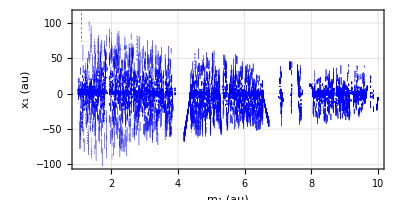

=== Alternative: ListPlot Version ===

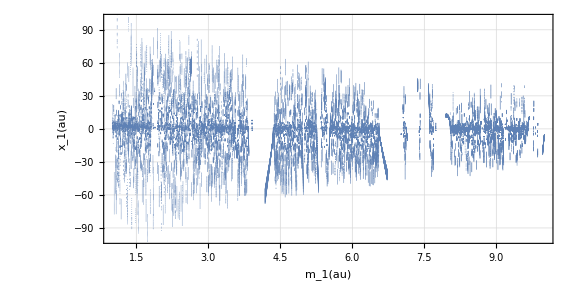

```mathematica
ClearAll["Global`*"];

(*Constants*)
G=4 Pi^2;
conv=1/(1.496*^8*365.25*24*3600);
seed=105;
epsilon=0.01; (*Softening parameter*)

(*Function to get local maxima of x1 position*)
getLocalMaxima[sol_,tStart_,tEnd_]:=Module[{x1Func,samples,peaks},x1Func=x1/. sol[[1]];
(*Sample the function densely*)samples=Table[{t,x1Func[t]},{t,tStart,tEnd,0.1}];
(*Find local maxima by checking neighbors*)peaks=Select[Range[2,Length[samples]-1],samples[[#,2]]>samples[[#-1,2]]&&samples[[#,2]]>samples[[#+1,2]]&];
(*Return the x1 values at peaks*)samples[[peaks,2]]]

(*Function to run simulation for given m1*)
runSimulation[mVar_]:=Module[{q2x,q2y,q3x,q3y,m1,m2,m3,pos1,vel1,pos2,vel2,pos3,vel3,eqs,init,sol,maxDist,maxima},SeedRandom[seed];
(*Initial conditions-fixed seed for reproducibility*)q2x=RandomReal[{5,20}];
q2y=RandomReal[{0,10}];
q3x=RandomReal[{-10,0}];
q3y=RandomReal[{5,20}];
m1=mVar;
m2=1;
m3=1;
(*Positions and velocities*)pos1={0,0};
vel1={0,10}*conv;
pos2={q2x,q2y};
vel2={-10,0}*conv;
pos3={q3x,q3y};
vel3={0,0};
(*Equations with softening*)eqs={x1''[t]==G*m2*(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),y1''[t]==G*m2*(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),x2''[t]==G*m1*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),y2''[t]==G*m1*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),x3''[t]==G*m1*(x1[t]-x3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2),y3''[t]==G*m1*(y1[t]-y3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2)};
(*Initial conditions*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve the system*)sol=Quiet@NDSolve[Join[eqs,init],{x1,y1,x2,y2,x3,y3},{t,0,100},MaxSteps->1000000,Method->"StiffnessSwitching",PrecisionGoal->8,AccuracyGoal->8];
(*If solution failed,return empty list*)If[sol==={},Return[{}]];
(*Check for escapes or extreme behavior*)maxDist=Quiet@Check[Max[Table[Sqrt[(x1[t]/. sol[[1]])^2+(y1[t]/. sol[[1]])^2]+Sqrt[(x2[t]/. sol[[1]])^2+(y2[t]/. sol[[1]])^2]+Sqrt[(x3[t]/. sol[[1]])^2+(y3[t]/. sol[[1]])^2],{t,80,100,2}]],Infinity];
If[maxDist>500,Return[{}]];(*System escaped*)(*Get local maxima of x1 position*)maxima=Quiet@Check[getLocalMaxima[sol,80,100],{}];
If[Length[maxima]==0,Return[{}]];
(*Filter extreme values*)maxima=Select[maxima,-200<=#<=200&];
(*Return points for bifurcation diagram*)Table[{mVar,max},{max,maxima}]]

(*Generate bifurcation data by varying m1*)
mRange=Range[1,10,0.001]; (*m1 from 1 to 10 in steps of 0.05*)
bifurcationData={};

Print["Generating bifurcation diagram..."];
Print["Varying m1 from ",First[mRange]," to ",Last[mRange]];
Print["Using seed: ",seed];
Print["Total parameter values: ",Length[mRange]];

progress=0;
Monitor[Do[data=runSimulation[mVar];
If[Length[data]>0,AppendTo[bifurcationData,data]];
progress++,{mVar,mRange}],ProgressIndicator[progress,{0,Length[mRange]}]];

(*Flatten the data*)
flatData=Flatten[bifurcationData,1];

Print["\nTotal points: ",Length[flatData]];

(*Create the bifurcation diagram*)
bifurcationPlot=Graphics[{PointSize[0.0003],Blue,Point[flatData]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(1\)]\) (au)",FontSize->14, Italic],Style["\!\(\*SubscriptBox[\(x\), \(1\)]\) (au)",FontSize->14, Italic]},PlotRange->{{1,10},Automatic},AspectRatio->1/2,GridLines->Automatic];

Print["\n=== Bifurcation Diagram (Local Maxima Method) ==="];
bifurcationPlot

(*Optional:Create alternative visualization with ListPlot*)


listPlotVersion=ListPlot[flatData,PlotStyle->{PointSize[0.0003]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["m_1(au)",Italic,FontSize->14],Style["x_1(au)",Italic,FontSize->14]},GridLines->Automatic,PlotRange->{{1,10},{100,-100}},(*inverted y-axis*)AspectRatio->1/2,ImageSize->Large,Joined->False];

Print["\n=== Alternative: ListPlot Version ==="];
listPlotVersion
```

Generating bifurcation diagram...

Varying m1 from 1. to 10.

Using seed: 121

Total parameter values: 9001

Total points: 100346

=== Bifurcation Diagram (Local Maxima Method) ===

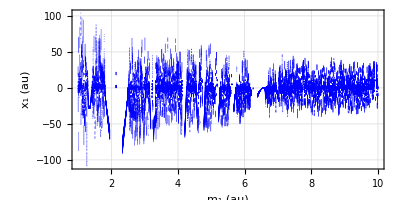

=== Alternative: ListPlot Version ===

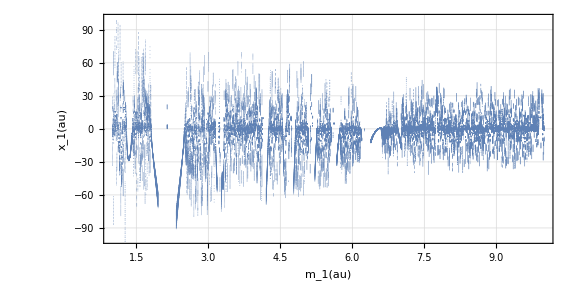

```mathematica
ClearAll["Global`*"];

(*Constants*)
G=4 Pi^2;
conv=1/(1.496*^8*365.25*24*3600);
seed=121;
epsilon=0.01; (*Softening parameter*)

(*Function to get local maxima of x1 position*)
getLocalMaxima[sol_,tStart_,tEnd_]:=Module[{x1Func,samples,peaks},x1Func=x1/. sol[[1]];
(*Sample the function densely*)samples=Table[{t,x1Func[t]},{t,tStart,tEnd,0.1}];
(*Find local maxima by checking neighbors*)peaks=Select[Range[2,Length[samples]-1],samples[[#,2]]>samples[[#-1,2]]&&samples[[#,2]]>samples[[#+1,2]]&];
(*Return the x1 values at peaks*)samples[[peaks,2]]]

(*Function to run simulation for given m1*)
runSimulation[mVar_]:=Module[{q2x,q2y,q3x,q3y,m1,m2,m3,pos1,vel1,pos2,vel2,pos3,vel3,eqs,init,sol,maxDist,maxima},SeedRandom[seed];
(*Initial conditions-fixed seed for reproducibility*)q2x=RandomReal[{5,20}];
q2y=RandomReal[{0,10}];
q3x=RandomReal[{-10,0}];
q3y=RandomReal[{5,20}];
m1=mVar;
m2=1;
m3=1;
(*Positions and velocities*)pos1={0,0};
vel1={0,10}*conv;
pos2={q2x,q2y};
vel2={-10,0}*conv;
pos3={q3x,q3y};
vel3={0,0};
(*Equations with softening*)eqs={x1''[t]==G*m2*(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),y1''[t]==G*m2*(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+epsilon^2)^(3/2),x2''[t]==G*m1*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),y2''[t]==G*m1*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2+epsilon^2)^(3/2)+G*m3*(y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+epsilon^2)^(3/2),x3''[t]==G*m1*(x1[t]-x3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2),y3''[t]==G*m1*(y1[t]-y3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2+epsilon^2)^(3/2)+G*m2*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2+epsilon^2)^(3/2)};
(*Initial conditions*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve the system*)sol=Quiet@NDSolve[Join[eqs,init],{x1,y1,x2,y2,x3,y3},{t,0,100},MaxSteps->1000000,Method->"StiffnessSwitching",PrecisionGoal->8,AccuracyGoal->8];
(*If solution failed,return empty list*)If[sol==={},Return[{}]];
(*Check for escapes or extreme behavior*)maxDist=Quiet@Check[Max[Table[Sqrt[(x1[t]/. sol[[1]])^2+(y1[t]/. sol[[1]])^2]+Sqrt[(x2[t]/. sol[[1]])^2+(y2[t]/. sol[[1]])^2]+Sqrt[(x3[t]/. sol[[1]])^2+(y3[t]/. sol[[1]])^2],{t,80,100,2}]],Infinity];
If[maxDist>500,Return[{}]];(*System escaped*)(*Get local maxima of x1 position*)maxima=Quiet@Check[getLocalMaxima[sol,80,100],{}];
If[Length[maxima]==0,Return[{}]];
(*Filter extreme values*)maxima=Select[maxima,-200<=#<=200&];
(*Return points for bifurcation diagram*)Table[{mVar,max},{max,maxima}]]

(*Generate bifurcation data by varying m1*)
mRange=Range[1,10,0.001]; (*m1 from 1 to 10 in steps of 0.05*)
bifurcationData={};

Print["Generating bifurcation diagram..."];
Print["Varying m1 from ",First[mRange]," to ",Last[mRange]];
Print["Using seed: ",seed];
Print["Total parameter values: ",Length[mRange]];

progress=0;
Monitor[Do[data=runSimulation[mVar];
If[Length[data]>0,AppendTo[bifurcationData,data]];
progress++,{mVar,mRange}],ProgressIndicator[progress,{0,Length[mRange]}]];

(*Flatten the data*)
flatData=Flatten[bifurcationData,1];

Print["\nTotal points: ",Length[flatData]];

(*Create the bifurcation diagram*)
bifurcationPlot=Graphics[{PointSize[0.0003],Blue,Point[flatData]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(1\)]\) (au)",FontSize->14, Italic],Style["\!\(\*SubscriptBox[\(x\), \(1\)]\) (au)",FontSize->14, Italic]},PlotRange->{{1,10},Automatic},AspectRatio->1/2,GridLines->Automatic];

Print["\n=== Bifurcation Diagram (Local Maxima Method) ==="];
bifurcationPlot

(*Optional:Create alternative visualization with ListPlot*)


listPlotVersion=ListPlot[flatData,PlotStyle->{PointSize[0.0003]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["m_1(au)",Italic,FontSize->14],Style["x_1(au)",Italic,FontSize->14]},GridLines->Automatic,PlotRange->{{1,10},{100,-100}},(*inverted y-axis*)AspectRatio->1/2,ImageSize->Large,Joined->False];

Print["\n=== Alternative: ListPlot Version ==="];
listPlotVersion
```